```mathematica
(* https://mathematica.stackexchange.com/questions/261561/generating-1-f-noise *)
(* Timmer Konig 1995 *)
(* astrochron/R/FUNCTION-makeNoise_v3.R *)
```

```mathematica
nn=2^16 (*Number of spectral points*)
S[f_]:=1/f;
s1=Table[If[f!=nn/2,
(RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]]),
RandomVariate[NormalDistribution[]]]*
 Sqrt[S[f]/2],{f,1,nn/2 }];
s2=Join[{0},s1,Reverse[Conjugate[s1[[1;;-2]]]]];
pwr=s2.Conjugate[s2];
norm=1/Sqrt[pwr];
```

65536

{0.002508,Null}

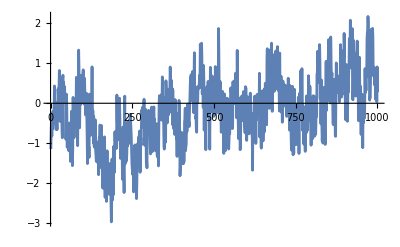

```mathematica
Timing[if=InverseFourier[s2,FourierParameters->{-1,-1}];]
l=Chop[norm if];
ListLinePlot[Take[l,UpTo[1000]]]
```

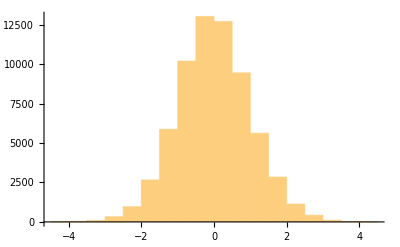

5.82867×10^-16

1.00001

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.859596},{2,0.792806},{3,0.761108},{4,0.735802},{5,0.716868},{6,0.702068},{7,0.689918},{8,0.678587},{9,0.668475},{10,0.657876},{11,0.6504},{12,0.641508},{13,0.634781},{14,0.627731},{15,0.621084},{16,0.616084},{17,0.609914},{18,0.604551},{19,0.600064},{20,0.594696},{21,0.591145},{22,0.585729},{23,0.581602},{24,0.578401},{25,0.573063},{26,0.56975},{27,0.565996},{28,0.564684},{29,0.561488},{30,0.558405},{31,0.555136},{32,0.550587},{33,0.546347},{34,0.54308},{35,0.53938},{36,0.534643},{37,0.532728},{38,0.531316},{39,0.528316},{40,0.526723},{41,0.526144},{42,0.524255},{43,0.521538},{44,0.517775},{45,0.515535},{46,0.514015},{47,0.511042},{48,0.508638},{49,0.507129},{50,0.50488},{51,0.503769},{52,0.502923},{53,0.500724},{54,0.49913},{55,0.497563},{56,0.495401},{57,0.494589},{58,0.493424},{59,0.492496},{60,0.490538},{61,0.489115},{62,0.486978},{63,0.486635},{64,0.484789},{65,0.483499},{66,0.480621},{67,0.477625},{68,0.476433},{69,0.474916},{70,0.473955},{71,0.472428},{72,0.470797},{73,0.468544},{74,0.466129},{75,0.46419},{76,0.461786},{77,0.459303},{78,0.458361},{79,0.456527},{80,0.455547},{81,0.454728},{82,0.452997},{83,0.450639},{84,0.448173},{85,0.44591},{86,0.442949},{87,0.441243},{88,0.441654},{89,0.441778},{90,0.441214},{91,0.442249},{92,0.443965},{93,0.442878},{94,0.442487},{95,0.442637},{96,0.442073},{97,0.440831},{98,0.438778},{99,0.436288},{100,0.433394}}

{a→0.873046,b→0.0942588}

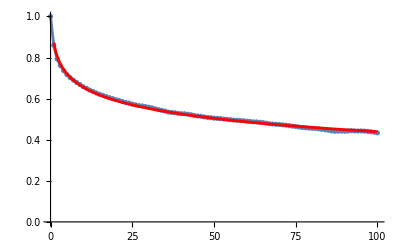

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

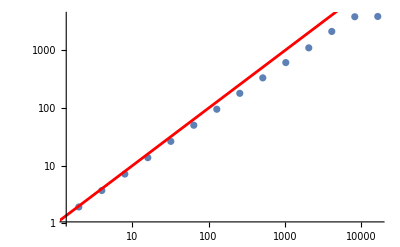

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

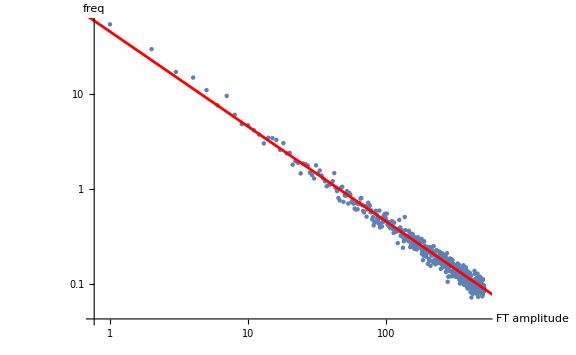

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"FT amplitude","freq"},LabelStyle->Larger];
pft2=LogLogPlot[{45/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```